```mathematica
Wpdata=RandomVariate[NormalDistribution[7 10^9, 2/100 7 10^9],1000];
Crdata = RandomVariate[NormalDistribution[0.0001, 0.25 0.0001], 1000];
Midata = RandomVariate[NormalDistribution[0.0001, 0.25 0.0001], 1000];
Tkdata = RandomVariate[LogNormalDistribution[ -2, 0.25 2], 1000];
Fodata = RandomVariate[LogNormalDistribution[ 2.5, 0.25 2.5], 1000];
Fidata = RandomVariate[LogNormalDistribution[ 2.5, 0.25 2.5], 1000];
Dtdata = RandomVariate[UniformDistribution[{0.85, 0.99}], 1000];
Audata = RandomVariate[NormalDistribution[0.01, 12.5/100 0.01],1000];
```

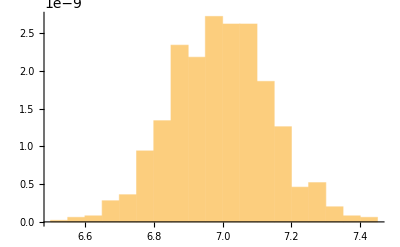

```mathematica
Histogram[Wpdata,20,"PDF"]
```

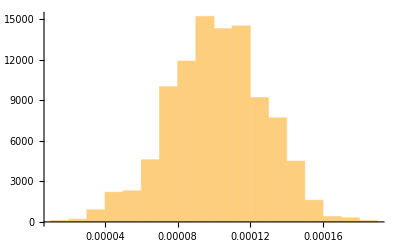

```mathematica
Histogram[Crdata,20, "PDF"]
```

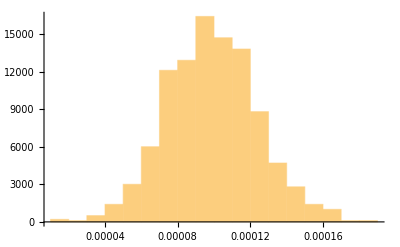

```mathematica
Histogram[Midata,20,"PDF"]
```

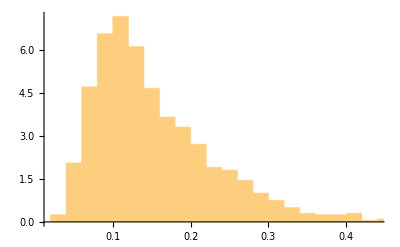

```mathematica
Histogram[Tkdata, 20, "PDF"]
```

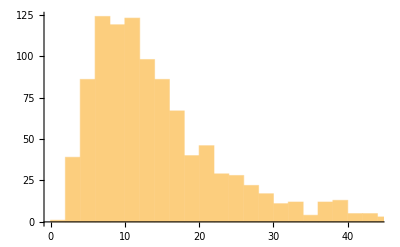

```mathematica
Histogram[Fodata]
```

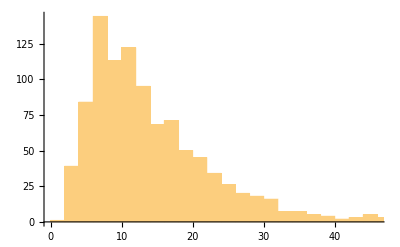

```mathematica
Histogram[Fidata]
```

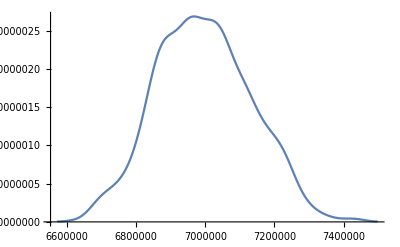

```mathematica
SmoothHistogram[Wpdata]
```

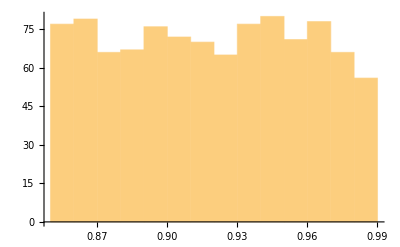

```mathematica
Histogram[Dtdata]
```

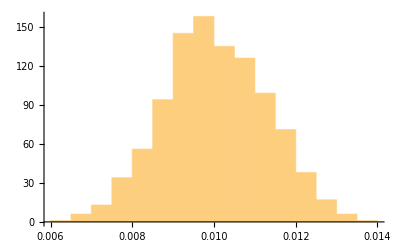

```mathematica
Histogram[Audata]
```

```mathematica
FlakeModel =Wpdata (Crdata + Midata)Tkdata Fodata Fidata Dtdata Audata;
```

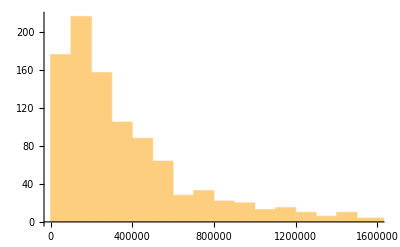

```mathematica
Histogram[FlakeModel]
```

```mathematica
Plot[CDF[FlakeModel,x],{x,0, 2 10^6}]
```

-Graphics-

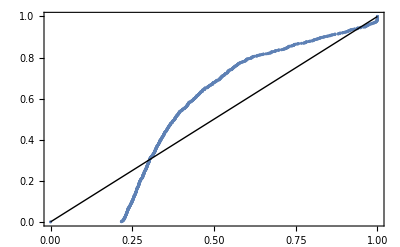

```mathematica
ProbabilityPlot[FlakeModel]
```

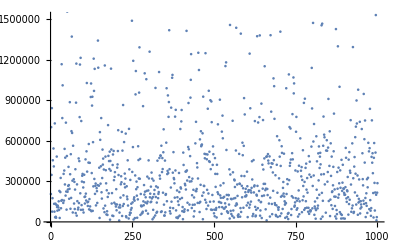

```mathematica
ListPlot[FlakeModel]
```

```mathematica
HistogramDistribution[FlakeModel]
```

DataDistribution[…]

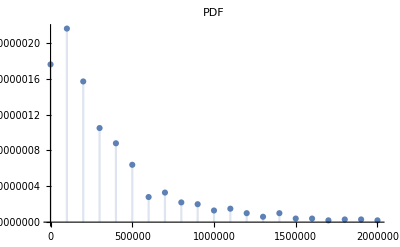
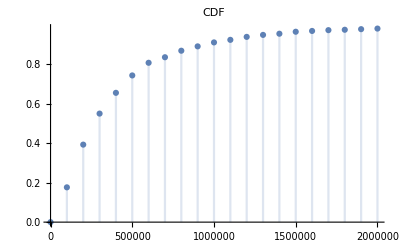

```mathematica
DiscretePlot[#[HistogramDistribution[FlakeModel],x],{x,0, 2 10^6, 10^5}, PlotLabel->#]&/@{PDF,CDF}
```

```mathematica
distro = HistogramDistribution[FlakeModel]
```

DataDistribution[…]

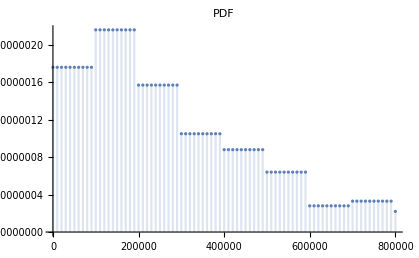
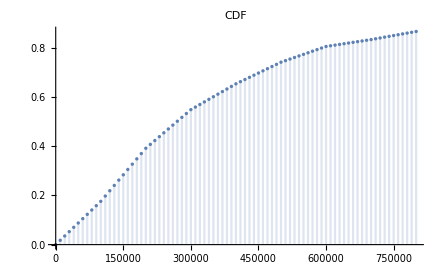

```mathematica
DiscretePlot[#[HistogramDistribution[FlakeModel],x],{x,0, 0.8 10^6, 10^4}, PlotLabel->#]&/@{PDF,CDF}
```